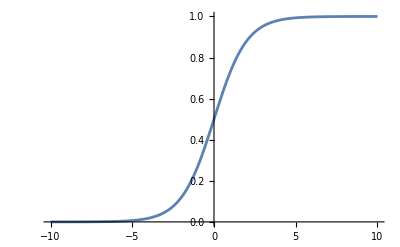

```mathematica
Plot[1 - 1/(1+Exp[X]),{X,-10,10}]
```

```mathematica
clin[mu_] = 4*(2+Sqrt[1+6*mu])Sqrt[-1 + Sqrt[1+6mu]]/(3Sqrt[3]);
d[nu_,lam_,c_,mu_] = -(1+nu^2)^2 + mu + c nu - lam;
SOL[mu_]=FullSimplify[nu/.Solve[D[d[nu,lam,clin[mu],mu],nu]==0,nu]]
```

{(2-2^(1/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3))/(2^(2/3) √3 (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(1/3)),(-6 ⅈ-2 √3-3 ⅈ 2^(1/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3)+2^(1/3) √3 (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3))/(6 2^(2/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(1/3)),(6 ⅈ-2 √3+3 ⅈ 2^(1/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3)+2^(1/3) √3 (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3))/(6 2^(2/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(1/3))}

```mathematica
Solve[d[SOL[0.25][[3]],lam,clin[0.25],0.25]==0,lam]
```

{{lam→-1.38778×10^-16+2.15779 ⅈ}}

```mathematica
2.1577916296081474
```

```mathematica
SOL[0.25]
```

{0.440128,-0.220064-1.07018 ⅈ,-0.220064+1.07018 ⅈ}

```mathematica
1.0701797547706868/(2.1577916296081474/clin[0.25])
```

1.04228

```mathematica
FullSimplify[-((2 2^(1/3) (1+ⅈ √3))/(-384 √3 √(-1+√(1+6 mu))-192 √3 √(1+6 mu) √(-1+√(1+6 mu))+√(442368+(-384 √3 √(-1+√(1+6 mu))-192 √3 √(1+6 mu) √(-1+√(1+6 mu)))^2))^(1/3))+1/(24 2^(1/3))(1-ⅈ √3) (-384 √3 √(-1+√(1+6 mu))-192 √3 √(1+6 mu) √(-1+√(1+6 mu))+√(442368+(-384 √3 √(-1+√(1+6 mu))-192 √3 √(1+6 mu) √(-1+√(1+6 mu)))^2))^(1/3)]
```

```mathematica
nu[mu_]=(-6 ⅈ-2 √3-3 ⅈ 2^(1/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3)+2^(1/3) √3 (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3))/(6 2^(2/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(1/3))
```

(-6 ⅈ-2 √3-3 ⅈ 2^(1/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3)+2^(1/3) √3 (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(2/3))/(6 2^(2/3) (-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(1/3))

```mathematica
FullSimplify[-((2 2^(1/3) (1-ⅈ √3))/(-384 √3 √(-1+√(1+6 mu))-192 √3 √(1+6 mu) √(-1+√(1+6 mu))+√(442368+(-384 √3 √(-1+√(1+6 mu))-192 √3 √(1+6 mu) √(-1+√(1+6 mu)))^2))^(1/3))+1/(24 2^(1/3))(1+ⅈ √3) (-384 √3 √(-1+√(1+6 mu))-192 √3 √(1+6 mu) √(-1+√(1+6 mu))+√(442368+(-384 √3 √(-1+√(1+6 mu))-5192 √3 √(1+6 mu) √(-1+√(1+6 mu)))^2))]
```

-1/(3 2^(1/3))(3 ⅈ+√3) (48 √(-1+√(1+6 mu))+24 √(1+6 mu) √(-1+√(1+6 mu))-√(-358897+361201 √(1+6 mu)+3894 mu (-553+649 √(1+6 mu))))+Root-0.364+0.630 ⅈRoot[-4+27 #1^6&,4]-0.36370787865724047/(-2 √(-1+√(1+6 mu))-√(1+6 mu) √(-1+√(1+6 mu))+√((1+6 mu) (3+√(1+6 mu))))^(1/3)

```mathematica
nu[0.25]
```

-0.220064-1.07018 ⅈ

```mathematica
N[%]
```

-0.055016-0.267545 ⅈ→0.25

```mathematica
clin[0.25]
```

2.10155

```mathematica
ff[x_] = Exp[Min[(x-20)/0.1,500]];
ch[x_] = 1/(1+ff[x]);
```

```mathematica
Plot[ch[x],{x,-20,20}]
```

-Graphics-

```mathematica
ch[x_] = 1/(1+Exp[-(x-x0)/ep]);
chm[x_] = 1-ch[x];
Simplify[ch[x]chm[x]/ep - D[ch[x],x]]
Simplify[(2chm[x]^2 - chm[x])ch[x]/ep^2 - D[ch[x],{x,2}]]
Simplify[(6chm[x]^3 - 6chm[x]^2+chm[x])ch[x]/ep^3- D[ch[x],{x,3}]]
Simplify[(24chm[x]^4-36chm[x]^3 + 14chm[x]^2-chm[x])ch[x]/ep^4- D[ch[x],{x,4}]]
```

0

0

0

«1 more identical outputs»

```mathematica
ch[x_] = 1/(1+Exp[(x)/ep]);
chm[x_] = 1-ch[x];
Simplify[-ch[x]chm[x]/ep - D[ch[x],x]]
Simplify[(2chm[x]^2 - chm[x])ch[x]/ep^2 - D[ch[x],{x,2}]]
Simplify[-(6chm[x]^3 - 6chm[x]^2+chm[x])ch[x]/ep^3- D[ch[x],{x,3}]]
Simplify[(24chm[x]^4-36chm[x]^3 + 14chm[x]^2-chm[x])ch[x]/ep^4- D[ch[x],{x,4}]]
```

0

0

0

«1 more identical outputs»

```mathematica
( - (l^4 D[c[x]u[x],{x,4}] + 2l^2  D[c[x]u[x],{x,2}]+c[x]u[x]) + cx l D[c[x]u[x],{x,1}]) -  c[x](-(l^4D[u[x],{x,4}] + 2l^2 D[u[x],{x,2}]+u[x])  + cx l D[u[x],{x,1}])
```

-c[x] u[x]+cx (u[x] c'[x]+c[x] u'[x])-6 c''[x] u''[x]-2 (2 c'[x] u'[x]+u[x] c''[x]+c[x] u''[x])-4 u'[x] c^(3)[x]-4 c'[x] u^(3)[x]-u[x] c^(4)[x]-c[x] (-u[x]+cx u'[x]-2 u''[x]-u^(4)[x])-c[x] u^(4)[x]

```mathematica
Collect[Simplify[%46],u[x]]
```

-6 c''[x] u''[x]-4 u'[x] c^(3)[x]-4 c'[x] (u'[x]+u^(3)[x])+u[x] (cx c'[x]-2 c''[x]-c^(4)[x])

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
n[u_] = -u^3;
Simplify[n[c ur + cp un + w] - c n[ur]]
```

c ur^3-(cp un+c ur+w)^3

```mathematica
Collect[D[c ur^3-(cp un+c ur+w)^3,w],w]
```

-3 (cp^2 un^2+2 c cp un ur+c^2 ur^2)-3 (2 cp un+2 c ur) w-3 w^2

```mathematica
cdb[nu_] = 4 nu (1+nu^2);
Collect[ d[nr+I ni,i w,c,mu],I]
```

mu+c (ⅈ ni+nr)-(1+(ⅈ ni+nr)^2)^2-i w

```mathematica
Reduce[Im[d[nr+I ni,I w,c,mu]],Element[nr|ni | w | c | mu,Reals]]
```

Reduce::naqs: (nr|ni|w|c|mu)∈&&Im[mu+c (ⅈ ni+nr)-(1+Power[«2»])^2]-Re[w] is not a quantified system of equations and inequalities.

Reduce[Im[mu+c (ⅈ ni+nr)-(1+(ⅈ ni+nr)^2)^2]-Re[w],(nr|ni|w|c|mu)∈ℝ]

```mathematica
d1[nu_,lam_,c_,mu_]=D[d[nu,lam,c,mu],nu]
```

c-4 nu (1+nu^2)

```mathematica
Expand[d[x+I y,I w,c,mu]]
```

```mathematica
Simplify[Re[-1+mu-ⅈ w+c x-2 x^2-x^4+ⅈ c y-4 ⅈ x y-4 ⅈ x^3 y+2 y^2+6 x^2 y^2+4 ⅈ x y^3-y^4],Element[x |y | c | w| mu,Reals]]
```

-1+mu+c x-2 x^2-x^4+2 y^2+6 x^2 y^2-y^4

```mathematica
Simplify[Im[-1+mu-ⅈ w+c x-2 x^2-x^4+ⅈ c y-4 ⅈ x y-4 ⅈ x^3 y+2 y^2+6 x^2 y^2+4 ⅈ x y^3-y^4],Element[x |y | c | w| mu,Reals]]
```

-w+y (c-4 (x+x^3-x y^2))

```mathematica
Simplify[Im[-1+mu-ⅈ w+c x-2 x^2-x^4+ⅈ c y-4 ⅈ x y-4 ⅈ x^3 y+2 y^2+6 x^2 y^2+4 ⅈ x y^3-y^4],Element[x |y | c | w| mu,Reals]]
```

```mathematica
dr[x_,y_,w_,c_,mu_] = Simplify[Re[Expand[d[x+I y,I w,c,mu]]],Element[x |y | c | w| mu,Reals]]
```

-1+mu+c x-2 x^2-x^4+2 y^2+6 x^2 y^2-y^4

```mathematica
di[x_,y_,w_,c_,mu_] = Simplify[Im[Expand[d[x+I y,I w,c,mu]]],Element[x |y | c | w| mu,Reals]]
```

-w+y (c-4 (x+x^3-x y^2))

```mathematica
ddr[x_,y_,w_,c_,mu_] = Simplify[Re[Expand[d1[x+I y,I w,c,mu]]],Element[x |y | c | w| mu,Reals]]
```

c-4 (x+x^3-3 x y^2)

```mathematica
ddi[x_,y_,w_,c_,mu_] = Simplify[Im[Expand[d1[x+I y,I w,c,mu]]],Element[x |y | c | w| mu,Reals]]
```

-4 (y+3 x^2 y-y^3)

```mathematica
NSolve[{dr[x,y,w,c,0.25]==0,di[x,y,w,c,0.25]==0,ddr[x,y,w,c,0.25]==0,ddi[x,y,w,c,0.25]==0},{x,y,w,c}]
```

{{x→-0.220064,y→1.07018,c→2.10155,w→2.15779},{x→0.220064,y→-1.07018,c→-2.10155,w→2.15779},{x→0.517293,y→0.,c→2.62286,w→0.},{x→-0.517293,y→0.,c→-2.62286,w→0.},{x→-0.220064,y→-1.07018,c→2.10155,w→-2.15779},{x→0.220064,y→1.07018,c→-2.10155,w→-2.15779},{x→0.+0.463783 ⅈ,y→-0.59558,c→0.-0.518029 ⅈ,w→0.+0.783835 ⅈ},{x→0.-0.463783 ⅈ,y→-0.59558,c→0.+0.518029 ⅈ,w→0.-0.783835 ⅈ},{x→0.+0.463783 ⅈ,y→0.59558,c→0.-0.518029 ⅈ,w→0.-0.783835 ⅈ},{x→0.-0.463783 ⅈ,y→0.59558,c→0.+0.518029 ⅈ,w→0.+0.783835 ⅈ},{x→0.+0.966571 ⅈ,y→0.,c→0.+0.254175 ⅈ,w→0.+0. ⅈ},{x→0.-0.966571 ⅈ,y→0.,c→0.-0.254175 ⅈ,w→0.+0. ⅈ}}